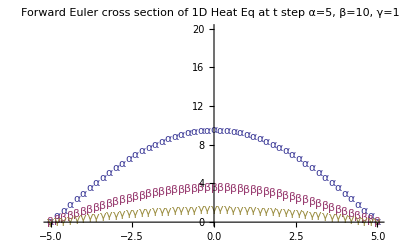

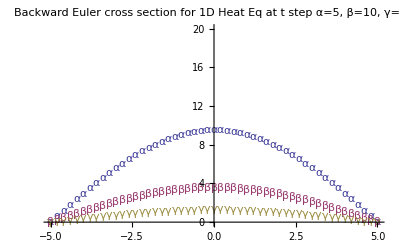

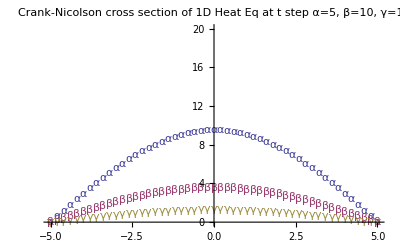

FE_500= {0.,0.596156,1.1876,1.77904,2.35641,2.93379,3.48798,4.04216,4.5644,5.08665,5.56871,6.05078,6.48507,6.91936,7.29904,7.67873,7.99784,8.31696,8.5705,8.82403,9.00802,9.19201,9.30356,9.41512,9.4525,9.48988,9.4525,9.41512,9.30356,9.19201,9.00802,8.82403,8.5705,8.31696,7.99784,7.67873,7.29904,6.91936,6.48507,6.05078,5.56871,5.08665,4.5644,4.04216,3.48798,2.93379,2.35641,1.77904,1.1876,0.596156,0.}

BE_500= {0.,0.596759,1.19116,1.78084,2.36347,2.93674,3.49839,4.0462,4.578,5.09169,5.58525,6.05672,6.50426,6.92609,7.32056,7.68613,8.02135,8.3249,8.59561,8.8324,9.03435,9.20067,9.33071,9.42396,9.48005,9.49878,9.48005,9.42396,9.33071,9.20067,9.03435,8.8324,8.59561,8.3249,8.02135,7.68613,7.32056,6.92609,6.50426,6.05672,5.58525,5.09169,4.578,4.0462,3.49839,2.93674,2.36347,1.78084,1.19116,0.596759,0.}

CR_500= {0.,0.596163,1.18997,1.77906,2.36111,2.93382,3.49492,4.04219,4.57347,5.08667,5.57975,6.05077,6.49788,6.91932,7.31343,7.67866,8.01357,8.31685,8.58731,8.82389,9.02566,9.19183,9.32175,9.41492,9.47097,9.48968,9.47097,9.41492,9.32175,9.19183,9.02566,8.82389,8.58731,8.31685,8.01357,7.67866,7.31343,6.91932,6.49788,6.05077,5.57975,5.08667,4.57347,4.04219,3.49492,2.93382,2.36111,1.77906,1.18997,0.596163,0.}

Glance at temperatures at the 500^th time step shows how Forward Euler is shows lower temperatures (overshoots), Backward Euler cools slower, and Crank-Nicolson falls in between and is more numerically stable.

```mathematica
Clear[M,Z,λ,x,i,Δx,Δt,t,X,Y,h,k,a,b,c]
x=-5.;
α=2.;
Δx=.2;
Δt=.01;
λ=(α*Δt)/Δx^2;
i=1;
While[x<5.,
	x=x+Δx;
	i++
	]
M=SparseArray[{Band[{1,1}]->1-2*λ, Band[{1,2}]->λ,Band[{2,1}]->λ},{i,i}];
M[[1,1]]=1.;
M[[1,2]]=0;
M[[i,i]]=1.;
M[[i,i-1]]=0;
Subscript[Temp, 0]=ConstantArray[20,i];
Subscript[Temp, 0]=ReplacePart[Subscript[Temp, 0],1->0];
Subscript[Temp, 0]=ReplacePart[Subscript[Temp, 0],i->0];
t=0;
While[t≤20/Δt,
		t++;
		Subscript[Temp, t]=M.Subscript[Temp, t-1];
	];
f[h_,k_]={h,k};
Subscript[FE, 500]=Subscript[Temp, 500];
a=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 500]}];
b=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 1000]}];
c=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 1500]}];
ListPlot[{a,b,c},PlotMarkers->{"α","β","γ"},PlotRange->{0,20},PlotLabel->"Forward Euler cross section of 1D Heat Eq at t step α=5, β=10, γ=15"]
(*Start Backward Euler*)
Clear[M,Z,λ,x,i,Δx,Δt,t,X,Y,h,k,a,b,c,f]
x=-5.;
α=2.;
Δx=.2;
Δt=.01;
λ=(α*Δt)/Δx^2;
i=1;
While[x<5.,
	x=x+Δx;
	i++
	]
M=SparseArray[{Band[{1,1}]->1+2*λ, Band[{1,2}]->-λ,Band[{2,1}]->-λ},{i,i}];
M[[1,1]]=1.;
M[[1,2]]=0;
M[[i,i]]=1.;
M[[i,i-1]]=0;
Subscript[Temp, 0]=ConstantArray[20,i];
Subscript[Temp, 0]=ReplacePart[Subscript[Temp, 0],1->0];
Subscript[Temp, 0]=ReplacePart[Subscript[Temp, 0],i->0];
t=1;
While[t≤20/Δt,
		t++;
		Subscript[Temp, t]=LinearSolve[M,Subscript[Temp, t-1]];
	];
f[h_,k_]={h,k};
Subscript[BE, 500]=Subscript[Temp, 500];
a=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 500]}];
b=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 1000]}];
c=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 1500]}];
ListPlot[{a,b,c},PlotMarkers->{"α","β","γ"},PlotRange->{0,20},PlotLabel->"Backward Euler cross section for 1D Heat Eq at t step α=5, β=10, γ=15"]
(*Start Crank-Nicolson*)
Clear[M,Z,λ,x,i,Δx,Δt,t,X,Y,h,k,a,b,c,f,B,F]
x=-5.;
α=2.;
Δx=.2;
Δt=.01;
λ=(α*Δt)/Δx^2;
i=1;
While[x<5.,
	x=x+Δx;
	i++
	]
F=SparseArray[{Band[{1,1}]->2-2*λ, Band[{1,2}]->λ,Band[{2,1}]->λ},{i,i}];
F[[1,1]]=1.;
F[[1,2]]=0;
F[[i,i]]=1.;
F[[i,i-1]]=0;
Subscript[Temp, 0]=ConstantArray[20,i];
Subscript[Temp, 0]=ReplacePart[Subscript[Temp, 0],1->0];
Subscript[Temp, 0]=ReplacePart[Subscript[Temp, 0],i->0];
B=SparseArray[{Band[{1,1}]->2+2*λ, Band[{1,2}]->-λ,Band[{2,1}]->-λ},{i,i}];
B[[1,1]]=1.;
B[[1,2]]=0;
B[[i,i]]=1.;
B[[i,i-1]]=0;
Subscript[BTemp, 0]=ConstantArray[20,i];
Subscript[BTemp, 0]=ReplacePart[Subscript[BTemp, 0],1->0];
Subscript[BTemp, 0]=ReplacePart[Subscript[BTemp, 0],i->0];
X=F.Subscript[Temp, 0];
(*LinearSolve[B,X]*)
t=0;
While[t≤20/Δt,
		t++;
		V=F.Subscript[Temp, t-1];
		Subscript[Temp, t]=LinearSolve[B,V];
	];
f[h_,k_]={h,k};
Subscript[CR, 500]=Subscript[Temp, 500];
a=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 500]}];
b=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 1000]}];
c=MapThread[f,{Range[-5,5,.2],Subscript[Temp, 1500]}];
ListPlot[{a,b,c},PlotMarkers->{"α","β","γ"},PlotRange->{0,20},PlotLabel->"Crank-Nicolson cross section of 1D Heat Eq at t step α=5, β=10, γ=15"]
Print["FE_500= ",Subscript[FE, 500]]
Print["BE_500= ",Subscript[BE, 500]]
Print["CR_500= ",Subscript[CR, 500]]
Print["Glance at temperatures at the 500^th time step shows how Forward Euler is shows lower temperatures (overshoots), Backward Euler cools slower, and Crank-Nicolson falls in between and is more numerically stable."]
```